```mathematica
Clear["Global`*"]
```

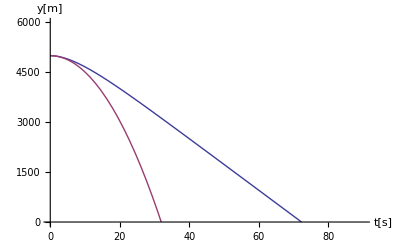
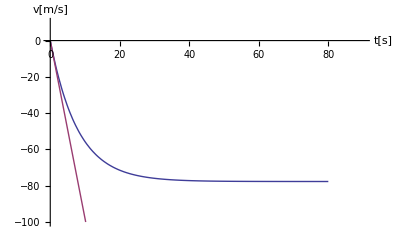
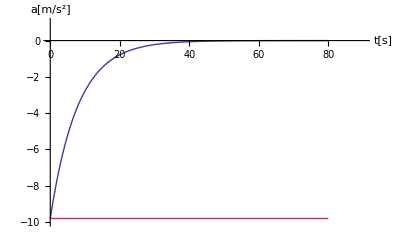
{-Graphics-Graphe comparant les positions y(t),-Graphics-Graphe comparant les vitesses y’(t),-Graphics-Graphe comparant les accélérations y’’(t)}

```mathematica
g=9.80665;
m=80;
k=10.1;
Vo=0;
Yo=5000;
yf[t_]:=(-g m^2)/k^2 ⅇ^(-k/m t)-(g m)/k t+(g m^2)/k^2+Yo;
vf[t_]:=(g m)/k ⅇ^(-k/m t)-(m g)/k;
af[t_]:=-g ⅇ^(-k/m t);
y[t_]:=-1/2 g t^2+Vo t+Yo;
v[t_]:=-g t + Vo;
a[t_]:=-g;
yyf=Labeled[Plot[{yf[t],y[t]},{t,0,80},
AxesLabel->{Style["t[s]",8],Style["y[m]",8]},AxesStyle->Arrowheads[{0.04}],PlotRange->{{0,90},{0,6000}}],Style["Graphe comparant les positions y(t)",7]];
vvf=Labeled[Plot[{vf[t],v[t]},{t,0,80},
AxesLabel->{Style["t[s]",8],Style["v[m/s]",8]},AxesStyle->Arrowheads[{0.04}],PlotRange->{{0,90},{-100,10}}],Style["Graphe comparant les vitesses y’(t)",7]];
aaf=Labeled[Plot[{af[t],a[t]},{t,0,80},
AxesLabel->{Style["t[s]",8],Style["a[m/s^2]",8]},AxesStyle->Arrowheads[{0.04}],PlotRange->{{0,90},{-10,1}}],Style["Graphe comparant les accélérations y’’(t)",7]];
{yyf,vvf,aaf}
```

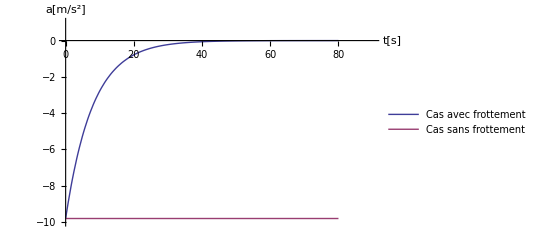
-Graphics-Graphe comparant les accélérations y’’(t)

```mathematica
Labeled[Plot[{af[t],a[t]},{t,0,80},
PlotLegends->{"Cas avec frottement","Cas sans frottement"},
AxesLabel->{Style["t[s]",8],Style["a[m/s^2]",8]},AxesStyle->Arrowheads[{0.04}],PlotRange->{{0,90},{-10,1}}],Style["Graphe comparant les accélérations y’’(t)",7]]
```

```mathematica
approx=Import["example.txt","List"]
```

{0.,-0.09800462156512245508687385109336531741064391098916530609130859375,«9996»,-77.67617953855796934792277141923477756790816783905029296875}

```mathematica
approx[[2]]
```

-0.09800462156512245508687385109336531741064391098916530609130859375

```mathematica
real=Table[vf[i],{i,0,100-0.01,0.01}]
```

{0.,-0.0980046,-0.195886,-0.293643,-0.391277,«9991»,-77.6762,-77.6762,-77.6762,-77.6762}

```mathematica
Length[real]
```

10000

```mathematica
Length[approx]
```

9999

```mathematica
delta=Table[Abs[real[[i]]-approx[[i]]],{i,1,9999,1}];
```

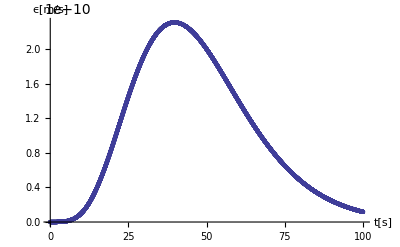

```mathematica
ListPlot[delta,DataRange->{0,100},AxesLabel->{Style["t[s]",8],Style["ϵ[m/s]",8]}]
```